# 3 - D spherical infinite Well

```mathematica
V[x,y,z]==0 (* for 0<x^2+y^2+z^2<a^2 )
```

```mathematica
(* the schrodinger equation is *)
-ℏ^2/(2m)∇^2 ψ[r,θ,ϕ]== Ε ψ[r,θ,ϕ]
```

```mathematica
(* seperating varible *)
ψ[r,θ,ϕ] ==R[r]Y[l,m,θ,ϕ]
```

```mathematica
(1/r^2∂/(∂r)(r^2∂/(∂r))-1/r^2 L^2)R[r]Y[l,m,θ,ϕ]==-(2m Ε)/ℏ^2 R[r]Y[l,m,θ,ϕ]
```

```mathematica
(* we have decoupled equation *)
(1/r^2 ⅆ/ⅆr(r^2 ⅆ/ⅆr)-(l(l+1))/r^2)R[r]==-(2m Ε)/ℏ^2 R[r]
L^2 Y[l,m,θ,ϕ]== l(l+1) Y[l,m,θ,ϕ]
```

```mathematica
Y[l_,m_,θ_,ϕ_]:=SphericalHarmonicY[l,m,θ,ϕ]
```

```mathematica
(* the solution of the radial part is *)
(1/r^2 ⅆ/ⅆr(r^2 ⅆ/ⅆr)-(l(l+1))/r^2)R[r]==-(2m Ε)/ℏ^2 R[r]
```

```mathematica
r^2(ⅆ^2 R)/(ⅆ r^2)+ 2 r ⅆR/ⅆr+( k^2 r^2-l(l+1))R==0
(* insert k = √((2mE)/ℏ^2) becomes *)
(kr)^2(ⅆ^2 R)/(ⅆ(kr)^2)+ 2 (kr) ⅆR/(ⅆ(kr))+( (kr)^2-l(l+1))R==0
(* the solution is the spherical Bessel function *)
```

```mathematica
R[l_,x_]:=SphericalBesselJ[l,x]
```

```mathematica
(* the solution is *)
ψ[r,θ,ϕ]==A R[l,k r]Y[l,m,θ,ϕ]==A SphericalBesselJ[l,k r]SphericalHarmonicY[l,m,θ,ϕ]
```

```mathematica
Table[{"l="<>ToString[l],FunctionExpand[SphericalBesselJ[l,x]]},{l,0,6}]//TableForm
```

l=0 | Sin[x]/x
l=1 | -Cos[x]/x+Sin[x]/x^2
l=2 | -(3 Cos[x])/x^2+((3-x^2) Sin[x])/x^3
l=3 | ((-15+x^2) Cos[x])/x^3-(3 (-5+2 x^2) Sin[x])/x^4
l=4 | (5 (-21+2 x^2) Cos[x])/x^4+((105-45 x^2+x^4) Sin[x])/x^5
l=5 | ((-945+105 x^2-x^4) Cos[x])/x^5+(15 (63-28 x^2+x^4) Sin[x])/x^6
l=6 | -(21 (495-60 x^2+x^4) Cos[x])/x^6+((10395-4725 x^2+210 x^4-x^6) Sin[x])/x^7

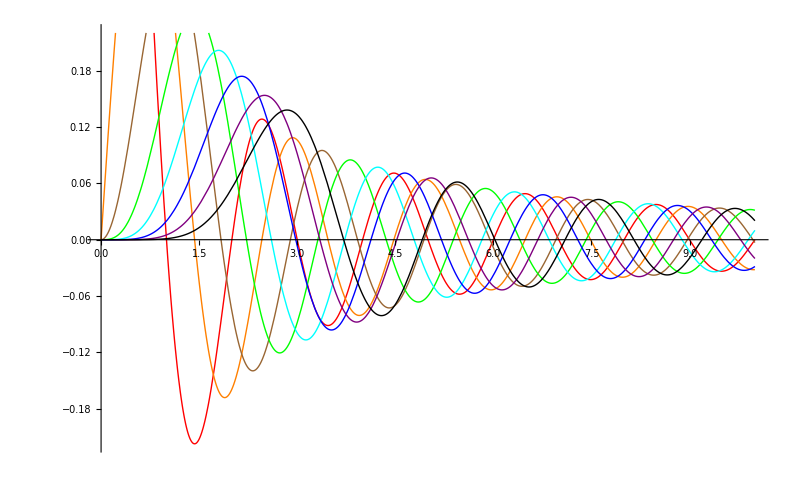

```mathematica
Plot[Evaluate[Table[SphericalBesselJ[l,π x],{l,0,7}]],{x,0,10},ImageSize->800,PlotStyle->{Red,Orange,Brown,Green, Cyan, Blue, Purple,Black}]
```

```mathematica
(* the BC fixed the wave function is zero at r =a *)
(* the root of Spherical Bessel J will determine the value of k and then the energy *)
(* the n-th root of SphericalBesselJ[l,x] is the n-orbit with angular momentum l *)
RootShift[l_,n_]:=Which[
l==0,0,
l==1,0.5,
l==2,0.9,
l==3,1.2,
l==4, 1.5,
l==5,If[n==1,2,2.2],
l==6,If[n==1,2.1,1]
]
SymbolAtomic[l_]:=Which[
l==0,"s",
l==1,"p",
l==2,"d",
l==3,"f",
l==4, "g",
l==5,"h",
l==6,"i"
]
RootSBJ[n_,l_]:=((x/.FindRoot[SphericalBesselJ[l,π x],{x,n+RootShift[l,n]}])π)
```

```mathematica
(* for orbit size 10^-15, the energy in eV *)
Energy[1,1] ℏ^2/(2mp 10^-30) 1/e
```

(4.18954×10^8 J^2 s^2)/(C kg)

```mathematica
EnergyLevel=Flatten[Table[{ToString[n]<>SymbolAtomic[l] ,(RootSBJ[n,l]/RootSBJ[1,0])^2},{n,1,5},{l,0,5}],1];
```

```mathematica
EnergyLevel2=Table[{(RootSBJ[n,l]/RootSBJ[1,0])^2,1},{l,0,6},{n,1,5}];
```

```mathematica
(* show the order of the energy level *)
SortedEnergyLevel=SortBy[EnergyLevel,Last]
```

{{1s,1.},{1p,2.04575},{1d,3.36563},{2s,4.},{1f,4.94763},{2p,6.0468},{1g,6.78389},{2d,8.38121},{1h,8.86877},{3s,9.},{2f,10.995},{3p,12.0471},{2g,13.8815},{3d,15.3861},{4s,16.},{2h,17.0352},{3f,19.0115},{4p,20.0472},{3g,22.918},{4d,24.3883},{5s,25.},{3h,27.101},{4f,29.0193},{5p,30.0472},{4g,33.9361},{5d,35.3895},{4h,39.1349},{5f,41.0236},{5g,46.9465},{5h,53.155}}

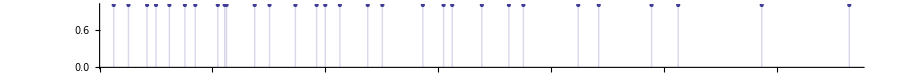

```mathematica
ListPlot[Table[{SortedEnergyLevel[[i]][[2]],1},{i,1,Length[SortedEnergyLevel]}],Filling->Axis,ImageSize->{900,100},PlotRange->{0,1},AspectRatio-> 1/12]
```

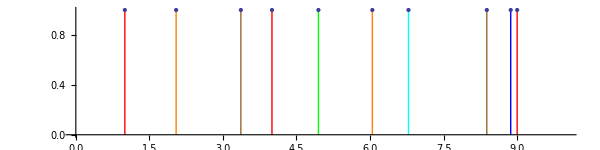

```mathematica
Show[
ListPlot[EnergyLevel2[[1]],Filling->Axis,ImageSize->{600,200},PlotRange->{{0,10},{0,1}},AspectRatio-> 1/4,FillingStyle->Red],
ListPlot[EnergyLevel2[[2]],Filling->Axis,AspectRatio-> 1/6,FillingStyle->Orange],
ListPlot[EnergyLevel2[[3]],Filling->Axis,AspectRatio-> 1/6,FillingStyle->Brown],
ListPlot[EnergyLevel2[[4]],Filling->Axis,AspectRatio-> 1/6,FillingStyle->Green],
ListPlot[EnergyLevel2[[5]],Filling->Axis,AspectRatio-> 1/6,FillingStyle->Cyan],
ListPlot[EnergyLevel2[[6]],Filling->Axis,AspectRatio-> 1/6,FillingStyle->Blue],
ListPlot[EnergyLevel2[[7]],Filling->Axis,AspectRatio-> 1/6,FillingStyle->Purple]
]
```

```mathematica
ListPlot[EnergyLevel2,Filling->Axis,ImageSize->{900,200},PlotRange->{{0,4.1},{0,1}},AspectRatio-> 1/6,PlotStyle->{Red,Orange,Brown,Green, Cyan, Blue, Purple}]
```

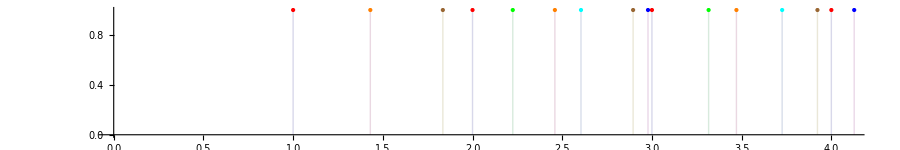

```mathematica
Table[FindRoot[SphericalBesselJ[0,π x],{x,n}],{n,1,5}]
Table[FindRoot[SphericalBesselJ[1,π x],{x,n+0.5}],{n,1,5}]
Table[FindRoot[SphericalBesselJ[2,π x],{x,n+0.9}],{n,1,5}]
Table[FindRoot[SphericalBesselJ[3,π x],{x,n+1.2}],{n,1,5}]
Table[FindRoot[SphericalBesselJ[4,π x],{x,n+1.5}],{n,1,5}]
Table[FindRoot[SphericalBesselJ[5,π x],{x,If[n==1,n+2,n+2.2]}],{n,1,5}]
```

{{x→1.},{x→2.},{x→3.},{x→4.},{x→5.}}

{{x→1.4303},{x→2.45902},{x→3.47089},{x→4.47741},{x→5.48154}}

{{x→1.83457},{x→2.89503},{x→3.92251},{x→4.93845},{x→5.94891}}

{{x→2.22433},{x→3.31587},{x→4.36022},{x→5.38696},{x→6.40497}}

{{x→2.60459},{x→3.72579},{x→4.78727},{x→5.82547},{x→6.85175}}

{{x→2.97805},{x→4.12737},{x→5.20587},{x→6.25579},{x→7.29074}}